# Hourglass Effect + Beam Divergence Effects

Looking at the Hourglass effect from a number of sources and understanding the longitudinal bunch and pulse shapes of the electron beam and laser at the ICS interaction point. Shows that a NEQ SR ICS suffers more from the hourglass effect than an ERL ICS due to the hourglass effect. Calculates reduction factors in both cases for circular beams, modifying M.A. Furman’s work to include a photon beam. The work by M.A. Furman is implemented currently using round beams, extending this to non-round beams is not trivial as it is not analytically tractable. Methods such as those by Miyahara, include the crossing angle effect and hourglass effect simultaneously and therefor offer a more full treatment of IP effects. These models however, are difficult to implement as again they are not analytically tractable.

## Units, Constants + Cases

```mathematica
(*Units*)
mm=10^-3;
cm=10^-2;
μm=10^-6;
nm=10^-9;
ps=10^-12;
fs=10^-15;
mrad=10^-3;
MeV=10^6;
```

```mathematica
(*Constants*)
c=299792458;
me=0.51099895MeV;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
CBETA150={Ee->(150MeV+me),ϕ->fivedeg,ϵn->0.3mm mrad,βIP->0.1262,σze->1mm,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
DIANA680={Ee->(680MeV+me),ϕ->fivedeg,ϵn->0.5mm mrad,βIP->20cm,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*5.7ps,npts->10000};
MAXIIIinjopt={Ee->(700MeV+me),ϕ->fivedeg,ϵn->1.398mm mrad,βIP->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*5.7ps,npts->10000};
```

```mathematica
(*CBETA Cases, Many pulse lengths*)
DIANA680ps10={Ee->(680MeV+me),ϕ->fivedeg,ϵn->0.5mm mrad,βIP->20cm,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*10ps,npts->10000};
DIANA680ps5={Ee->(680MeV+me),ϕ->fivedeg,ϵn->0.5mm mrad,βIP->20cm,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*5ps,npts->10000};
DIANA680ps1={Ee->(680MeV+me),ϕ->fivedeg,ϵn->0.5mm mrad,βIP->20cm,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*1ps,npts->10000};
DIANA680fs500={Ee->(680MeV+me),ϕ->fivedeg,ϵn->0.5mm mrad,βIP->20cm,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*500fs,npts->10000};
```

```mathematica
(*MAXIII Cases, Many pulse lengths*)
MAXIIIps10={Ee->(700MeV+me),ϕ->fivedeg,ϵn->1.398mm mrad,βIP->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
MAXIIIps5={Ee->(700MeV+me),ϕ->fivedeg,ϵn->1.398mm mrad,βIP->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*5ps,npts->10000};
MAXIIIps1={Ee->(700MeV+me),ϕ->fivedeg,ϵn->1.398mm mrad,βIP->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*1ps,npts->10000};
MAXIIIfs500={Ee->(700MeV+me),ϕ->fivedeg,ϵn->1.398mm mrad,βIP->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*500fs,npts->10000};
```

```mathematica
(*CBETA Cases, Many Spot Sizes*)
CBETAβ10={Ee->(150MeV+me),ϕ->fivedeg,ϵn->0.3mm mrad,βIP->61.26,σze->1mm,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
CBETAβ1={Ee->(150MeV+me),ϕ->fivedeg,ϵn->0.3mm mrad,βIP->0.6126,σze->1mm,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
CBETAβ01={Ee->(150MeV+me),ϕ->fivedeg,ϵn->0.3mm mrad,βIP->6.126mm,σze->1mm,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
```

## Intermediary Equations

```mathematica
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
ϵx[Ee_,ϵn_]:=ϵn/(β[Ee]*γ[Ee]);
w0[σL_]:=2*σL;
zr[λ_,σL_]:=(π*w0[σL]^2)/λ;
```

## Gaussian Beam Spread

```mathematica
βs[βIP_,z_]:=βIP*(1+(z/βIP)^2);
σe[βIP_,z_,Ee_,ϵn_]:=Sqrt[βs[βIP,z]*ϵx[Ee,ϵn]];
```

```mathematica
wz[σL_,z_,λ_]:=w0[σL]*Sqrt[1+(z/zr[λ,σL])^2];
```

## Beam and Pulse Envelope Plots (CBETA, ERL)

```mathematica
ElectronBeamSizeCBETA=Table[{z/mm,(σe[βIP,z,Ee,ϵn]/.CBETA150)/μm},{z,-(σze/.CBETA150)/2,(σze/.CBETA150)/2,σze/npts/.CBETA150}];
```

```mathematica
LaserPulseSizeCBETA=Table[{z/mm,(wz[σL,z,λ]/.CBETA150)/(2*μm)},{z,-(σzL/.CBETA150)/2,(σzL/.CBETA150)/2,σzL/npts/.CBETA150}];
```

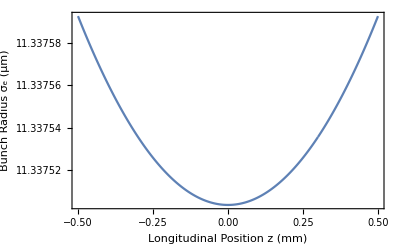

```mathematica
ListLinePlot[ElectronBeamSizeCBETA,Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch Radius σ_e (μm)"},LabelStyle->15]
```

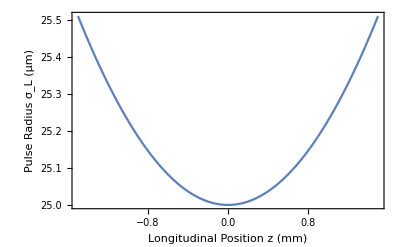

```mathematica
ListLinePlot[LaserPulseSizeCBETA,Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Pulse Radius σ_L (μm)"},LabelStyle->15]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

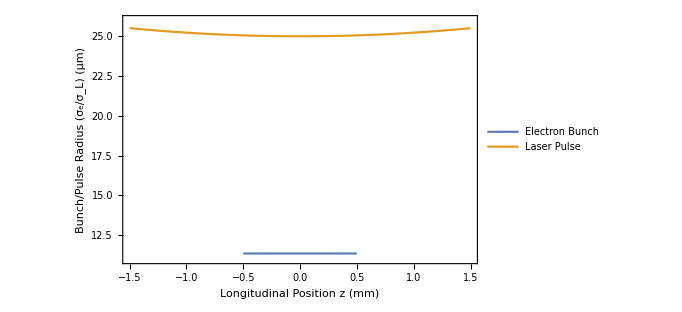

```mathematica
ListLinePlot[{ElectronBeamSizeCBETA,LaserPulseSizeCBETA},Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch/Pulse Radius (σ_e/σ_L) (μm)"},LabelStyle->15,PlotRange->{{-1.5,1.5},{11,26}},PlotLegends->Placed[LineLegend[{"Electron Bunch","Laser Pulse"},LabelStyle->12,LegendFunction->frame],{0.25,0.5}]]
```

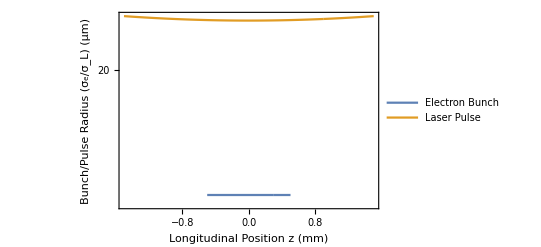

```mathematica
ListLogPlot[{ElectronBeamSizeCBETA,LaserPulseSizeCBETA},Joined->{True,True},Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch/Pulse Radius (σ_e/σ_L) (μm)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"Electron Bunch","Laser Pulse"},LabelStyle->12,LegendFunction->frame],{0.25,0.5}]]
```

## Beam and Pulse Envelope Plots (MAXIII, NEQ SR, Optimised injected parameters)

```mathematica
ElectronBeamSizeMAXIII=Table[{z/mm,(σe[βIP,z,Ee,ϵn]/.MAXIIIinjopt)/μm},{z,-(σze/.MAXIIIinjopt)/2,(σze/.MAXIIIinjopt)/2,σze/npts/.MAXIIIinjopt}];
```

```mathematica
LaserPulseSizeMAXIII=Table[{z/mm,(wz[σL,z,λ]/.MAXIIIinjopt)/(2*μm)},{z,-(σzL/.MAXIIIinjopt)/2,(σzL/.MAXIIIinjopt)/2,σzL/npts/.MAXIIIinjopt}];
```

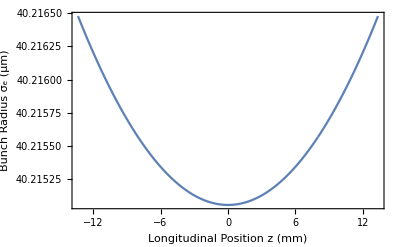

```mathematica
ListLinePlot[ElectronBeamSizeMAXIII,Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch Radius σ_e (μm)"},LabelStyle->15]
```

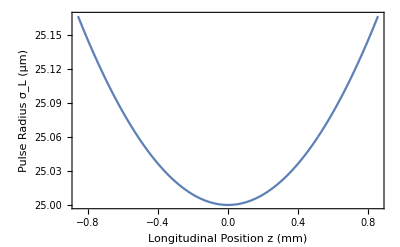

```mathematica
ListLinePlot[LaserPulseSizeMAXIII,Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Pulse Radius σ_L (μm)"},LabelStyle->15]
```

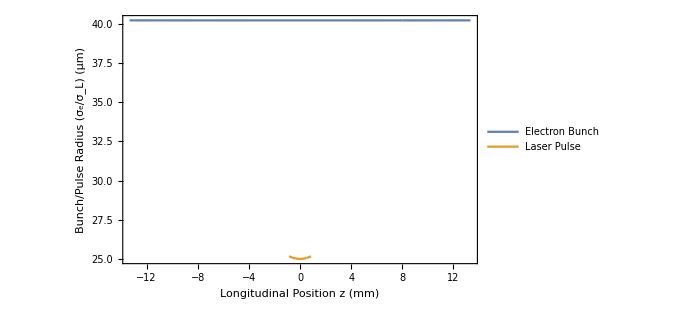

```mathematica
ListLinePlot[{ElectronBeamSizeMAXIII,LaserPulseSizeMAXIII},Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch/Pulse Radius (σ_e/σ_L) (μm)"},LabelStyle->15,PlotRange->Full,PlotLegends->Placed[LineLegend[{"Electron Bunch","Laser Pulse"},LabelStyle->12,LegendFunction->frame],{0.25,0.5}]]
```

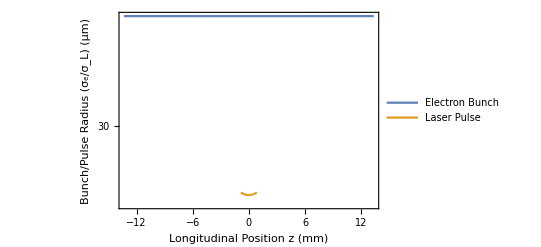

```mathematica
ListLogPlot[{ElectronBeamSizeMAXIII,LaserPulseSizeMAXIII},Joined->{True,True},Frame->True,FrameLabel->{"Longitudinal Position z (mm)", "Bunch/Pulse Radius (σ_e/σ_L) (μm)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"Electron Bunch","Laser Pulse"},LabelStyle->12,LegendFunction->frame],{0.25,0.5}]]
```

# Luminosity Crossing Angle Factor

There are two forms of the crossing angle reduction factor in T. Akagi, PRAB 19, 114701 (2016) Eq. 5 and Y. Miyahara, NIM A 588 (2008). Both retrieve identical results. This result confirms our co-ordinate systems are identical.

```mathematica
RACMiyahara[βIP_,z_,Ee_,ϵn_,σL_,ϕ_,σze_,σzL_]:=1/Sqrt[1+(σze^2+σzL^2)/(σe[βIP,z,Ee,ϵn]^2+σL^2)*Tan[ϕ/2]^2];
```

```mathematica
RACAkagi[βIP_,z_,Ee_,ϵn_,σL_,ϕ_,σze_,σzL_]:=(Sqrt[σe[βIP,z,Ee,ϵn]^2+σL^2]*Cos[ϕ/2])/Sqrt[(σe[βIP,z,Ee,ϵn]^2+σL^2)*Cos[ϕ/2]^2+(σze^2+σzL^2)*Sin[ϕ/2]^2];
```

```mathematica
RACdat=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETA150,RACAkagi[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETA150,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.DIANA680,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.MAXIIIinjopt},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

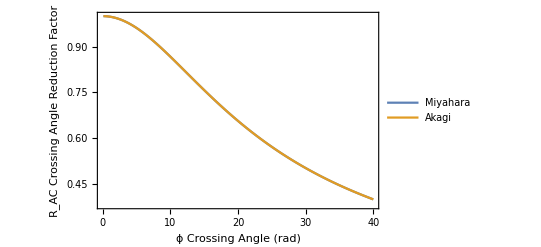

```mathematica
ListLinePlot[{Partition[Riffle[RACdat⟦All,1⟧,RACdat⟦All,2⟧],2],Partition[Riffle[RACdat⟦All,1⟧,RACdat⟦All,3⟧],2]},Frame->True,FrameLabel->{"ϕ Crossing Angle (rad)","R_AC Crossing Angle Reduction Factor"},PlotRange->{{0,40},{0.38,1}},LabelStyle->15,PlotLegends->Placed[LineLegend[{"Miyahara","Akagi"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

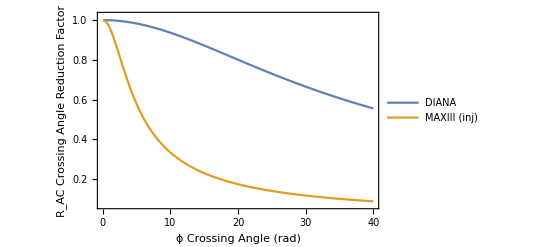

```mathematica
ListLinePlot[{Partition[Riffle[RACdat⟦All,1⟧,RACdat⟦All,4⟧],2],Partition[Riffle[RACdat⟦All,1⟧,RACdat⟦All,5⟧],2]},Frame->True,FrameLabel->{"ϕ Crossing Angle (rad)","R_AC Crossing Angle Reduction Factor"},PlotRange->{{0,40},{0.07,1.02}},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.78,0.3}]]
```

MAXIII has a faster decreasing crossing angle reduction factor R_AC because it has a much longer electron bunch length σ_ze.

```mathematica
RACTr=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETAβ10,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETAβ1,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETAβ01},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

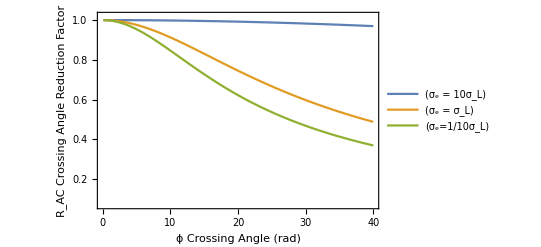

```mathematica
ListLinePlot[{Partition[Riffle[RACTr⟦All,1⟧,RACTr⟦All,2⟧],2],Partition[Riffle[RACTr⟦All,1⟧,RACTr⟦All,3⟧],2],Partition[Riffle[RACTr⟦All,1⟧,RACTr⟦All,4⟧],2]},Frame->True,FrameLabel->{"ϕ Crossing Angle (rad)","R_AC Crossing Angle Reduction Factor"},PlotRange->{{0,40},{0.07,1.02}},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.3,0.3}]]
```

This seems to suggest that as σ_e >> σ_L that the crossing angle reduction factor gets better.

# M.A. Furmann (Head-on, Round Beam)

## Analytical Solution (Round Beams)

```mathematica
Integrate[Exp[-t^2]/(1+t^2/trb^2),{t,-∞,∞},Assumptions->{Element[trb,Reals],trb>0}]/Sqrt[π]
```

ⅇ^(trb^2) √π trb Erfc[trb]

## Furman Intermediary

```mathematica
tRB[βIP_,z_,Ee_,ϵn_,σL_,σze_,σzL_,λ_]:=Sqrt[(2*(σe[βIP,z,Ee,ϵn]^2+σL^2))/((σze^2+σzL^2)*(σe[βIP,z,Ee,ϵn]^2/βIP^2+(4*σL)/zr[λ,σL]))];
```

```mathematica
tRB[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETA150
tRB[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680
tRB[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt
```

0.105539

0.162375

0.0215195

## Reduction Factor Calculation

```mathematica
RHG[βIP_,z_,Ee_,ϵn_,σL_,σze_,σzL_,λ_]:=Sqrt[π]*tRB[βIP,z,Ee,ϵn,σL,σze,σzL,λ]*Exp[tRB[βIP,z,Ee,ϵn,σL,σze,σzL,λ]^2]*Erfc[tRB[βIP,z,Ee,ϵn,σL,σze,σzL,λ]];
```

```mathematica
RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETA150
RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680
RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt
```

0.166715

0.241824

0.0372335

In comparing the optimised MAXIII with injected emittance parameters and the DIANA ERL parameters, it is possible to see that there is a ~6.5x larger hourglass reduction from the MAXIII case than in the DIANA case. This is mostly due to bunch length. The MAXIII ICS design is punished twice on longitudinal bunch size, by both non-zero crossing angle and the hourglass effect: it will have substantially reduced flux in comparison to the ERL case.

## R_HG Investigation (σ_ze,t_pulse vs σ_L)

```mathematica
RHGvsσzeDIANA=Table[{σze/mm,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680ps10,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680ps5,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680ps1,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680fs500},{σze,c*1ps,c*100ps,c*0.1ps}];
```

```mathematica
RHGvsσzeMAXIII=Table[{σze/mm,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIps10,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIps5,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIps1,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIfs500},{σze,c*1ps,c*200ps,c*0.1ps}];
```

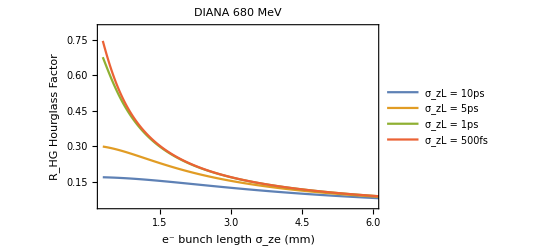

```mathematica
ListLinePlot[{Partition[Riffle[RHGvsσzeDIANA⟦All,1⟧,RHGvsσzeDIANA⟦All,2⟧],2],Partition[Riffle[RHGvsσzeDIANA⟦All,1⟧,RHGvsσzeDIANA⟦All,3⟧],2],Partition[Riffle[RHGvsσzeDIANA⟦All,1⟧,RHGvsσzeDIANA⟦All,4⟧],2],Partition[Riffle[RHGvsσzeDIANA⟦All,1⟧,RHGvsσzeDIANA⟦All,5⟧],2]},PlotRange->{{(c*1ps)/mm,(c*20ps)/mm},{0.05,0.8}},PlotLabel->"DIANA 680 MeV",Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"σ_zL = 10ps","σ_zL = 5ps","σ_zL = 1ps","σ_zL = 500fs"},LabelStyle->12,LegendFunction->frame],{0.7,0.6}]]
```

The hourglass factor R_HG shows the percentage of flux remaining i.e F = R_HG F. A higher R_HG is beneficial. From this plot it appears that reducing the pulse length of the laser is only beneficial with a small bunch length, the beneficial effect becomes negligible at ~15 ps.  This currently doesn’t take into account crossing angle effects.

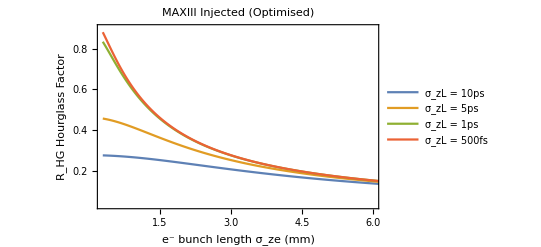

```mathematica
ListLinePlot[{Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,2⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,3⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,4⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,5⟧],2]},PlotRange->{{(c*1ps)/mm,(c*20ps)/mm},{0.032,0.9}},PlotLabel->"MAXIII Injected (Optimised)",Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"σ_zL = 10ps","σ_zL = 5ps","σ_zL = 1ps","σ_zL = 500fs"},LabelStyle->12,LegendFunction->frame],{0.75,0.7}]]
```

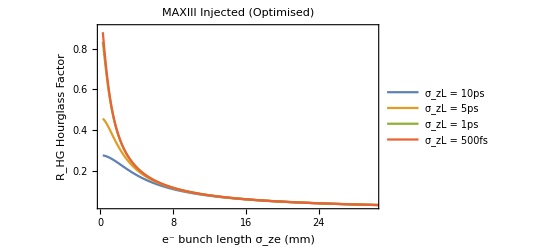

```mathematica
ListLinePlot[{Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,2⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,3⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,4⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,5⟧],2]},PlotRange->{{(c*1ps)/mm,(c*100ps)/mm},{0.032,0.9}},PlotLabel->"MAXIII Injected (Optimised)",Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"σ_zL = 10ps","σ_zL = 5ps","σ_zL = 1ps","σ_zL = 500fs"},LabelStyle->12,LegendFunction->frame],{0.75,0.7}]]
```

The electron bunch length σ_ze is long for the MAXIII case (89 ps vs 4 ps). Therefore, at their bunch lengths the hourglass reduction factor R_HG is much smaller and subsequently so is luminosity. The pulse length of the laser σ_zL is negligible in the operating regime of the

## R_HG Investigation (σ_e vs σ_ze) (Transverse Effects)

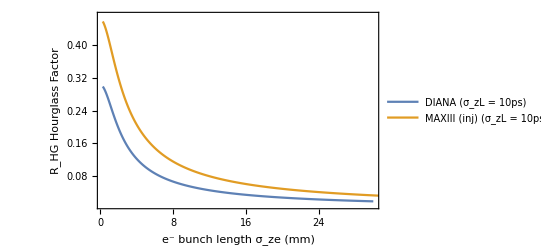

```mathematica
ListLinePlot[{Partition[Riffle[RHGvsσzeDIANA⟦All,1⟧,RHGvsσzeDIANA⟦All,3⟧],2],Partition[Riffle[RHGvsσzeMAXIII⟦All,1⟧,RHGvsσzeMAXIII⟦All,3⟧],2]},PlotRange->{{(c*1ps)/mm,(c*100ps)/mm},{0.01,0.47}},Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA (σ_zL = 10ps)","MAXIII (inj) (σ_zL = 10ps)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

This plot essentially shows the transverse effect of smaller beams in DIANA on the typically longitudinally dominant Hourglass effect. A smaller transverse size of the electron beam promotes a ~15% decrease in luminosity. This seems counterintuitive. The effect of transverse source size needs to be investigated in more detail.

```mathematica
RHGTr=Table[{σze/mm,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ10,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ1,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ01},{σze,c*1ps,c*100ps,c*0.1ps}];
```

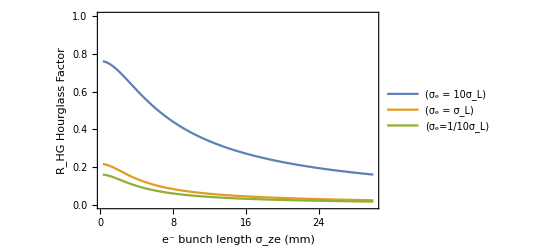

```mathematica
ListLinePlot[{Partition[Riffle[RHGTr⟦All,1⟧,RHGTr⟦All,2⟧],2],Partition[Riffle[RHGTr⟦All,1⟧,RHGTr⟦All,3⟧],2],Partition[Riffle[RHGTr⟦All,1⟧,RHGTr⟦All,4⟧],2]},PlotRange->{{(c*1ps)/mm,(c*100ps)/mm},{0,1}},Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

It appears from this plot that making the spot size of the electron beam much larger than the laser pulse spot size means that a much larger fraction of the photons are retained. This is also the

## R_AC×R_HG Approximate Angular + Hourglass Correction (DIANA vs MAXIII NEQ)

```mathematica
RHGRACvsϕ=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

```mathematica
RHGRACvsσze=Table[{σze/mm,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.DIANA680,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt},{σze,c*0.1ps,c*100ps,c*0.1ps}];
```

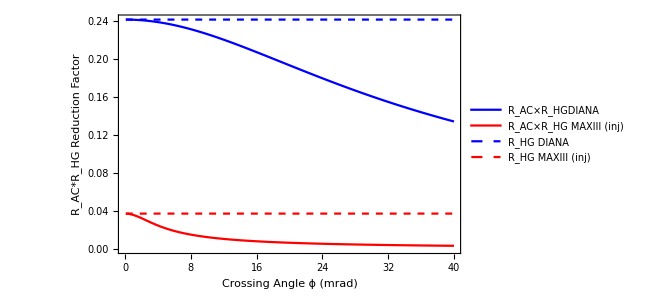

```mathematica
ListLinePlot[{Partition[Riffle[RHGRACvsϕ⟦All,1⟧,RHGRACvsϕ⟦All,2⟧],2],Partition[Riffle[RHGRACvsϕ⟦All,1⟧,RHGRACvsϕ⟦All,3⟧],2],Partition[Riffle[RHGRACvsϕ⟦All,1⟧,RHGRACvsϕ⟦All,4⟧],2],Partition[Riffle[RHGRACvsϕ⟦All,1⟧,RHGRACvsϕ⟦All,5⟧],2]},PlotRange->Full,Frame->True,FrameLabel->{"Crossing Angle ϕ (mrad)","R_AC*R_HG Reduction Factor"},LabelStyle->15,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[LineLegend[{"R_AC×R_HGDIANA","R_AC×R_HG MAXIII (inj)","R_HG DIANA","R_HG MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.25,0.5}]]
```

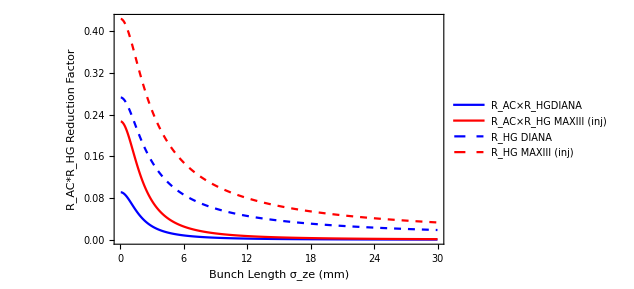

```mathematica
ListLinePlot[{Partition[Riffle[RHGRACvsσze⟦All,1⟧,RHGRACvsσze⟦All,2⟧],2],Partition[Riffle[RHGRACvsσze⟦All,1⟧,RHGRACvsσze⟦All,3⟧],2],Partition[Riffle[RHGRACvsσze⟦All,1⟧,RHGRACvsσze⟦All,4⟧],2],Partition[Riffle[RHGRACvsσze⟦All,1⟧,RHGRACvsσze⟦All,5⟧],2]},PlotRange->Full,Frame->True,FrameLabel->{"Bunch Length σ_ze (mm)","R_AC*R_HG Reduction Factor"},LabelStyle->15,PlotStyle->{Blue,Red,{Blue,Dashed},{Red,Dashed}},PlotLegends->Placed[LineLegend[{"R_AC×R_HGDIANA","R_AC×R_HG MAXIII (inj)","R_HG DIANA","R_HG MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

The R_AC dependence isn’t shown on these plots as it goes from 1 to 0 and would obscure the more important data. For this information consult an earlier plot.

The Miyahara paper (Y. Miyahara, NIM A 588 (2008)) show the reduction factor against crossing angle for a number of treatments. The reduction factor can be composed of the hourglass effect (HG) and a crossing angle effect (AC).  The main point is to show that R_AC*R_HG overestimates the reduction factor in comparison to a full treatment R_ACHG. Miyahara makes a factor of 2 error in tx^2 though, so this plot may be wrong. Coincidentally Miyahara worked on this for the NewSUBARU ICS.

## R_AC×R_HG Approximate Angular + Hourglass Correction (Transverse Beam Size)

```mathematica
RACRHGTrϕ=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ10,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ1,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ01},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

```mathematica
RACRHGTrσze=Table[{σze/mm,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ10,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ1,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETAβ01},{σze,c*0.1ps,c*100ps,c*0.1ps}];
```

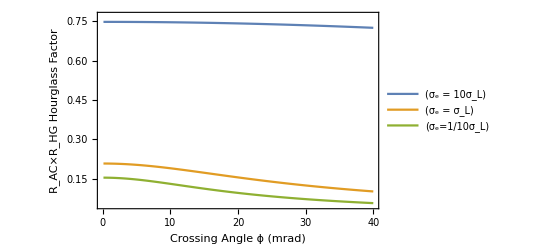

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGTrϕ⟦All,1⟧,RACRHGTrϕ⟦All,2⟧],2],Partition[Riffle[RACRHGTrϕ⟦All,1⟧,RACRHGTrϕ⟦All,3⟧],2],Partition[Riffle[RACRHGTrϕ⟦All,1⟧,RACRHGTrϕ⟦All,4⟧],2]},PlotRange->{{0,40},{0.05,0.77}},Frame->True,FrameLabel->{"Crossing Angle ϕ (mrad)","R_AC×R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.7,0.6}]]
```

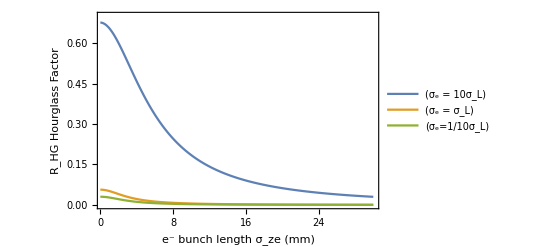

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGTrσze⟦All,1⟧,RACRHGTrσze⟦All,2⟧],2],Partition[Riffle[RACRHGTrσze⟦All,1⟧,RACRHGTrσze⟦All,3⟧],2],Partition[Riffle[RACRHGTrσze⟦All,1⟧,RACRHGTrσze⟦All,4⟧],2]},PlotRange->{{(c*1ps)/mm,(c*100ps)/mm},{0,0.7}},Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_HG Hourglass Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

## Transverse Effect (R_AC×R_HG×L_0) (Corrections Plus Original Dependence) (DIANA vs MAXIII)

L0Tr is the transverse component of the luminosity. This needs to be included in order to evaluate transverse beam and pulse sizes correctly.

```mathematica
L0Tr[βIP_,z_,Ee_,ϵn_,σL_]:=1/(σe[βIP,z,Ee,ϵn]^2+σL^2);
```

```mathematica
RACRHGL0ϕ=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.DIANA680,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.MAXIIIinjopt},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

```mathematica
RACRHGL0σze=Table[{σze/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.DIANA680,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.MAXIIIinjopt},{σze,c*0.1ps,c*100ps,c*0.1ps}];
```

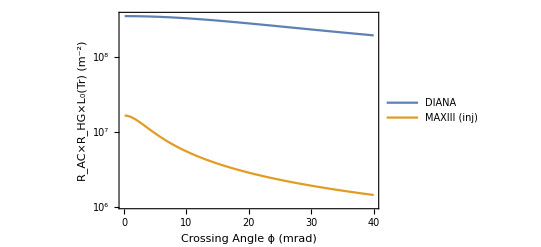

```mathematica
ListLogPlot[{Partition[Riffle[RACRHGL0ϕ⟦All,1⟧,RACRHGL0ϕ⟦All,2⟧],2],Partition[Riffle[RACRHGL0ϕ⟦All,1⟧,RACRHGL0ϕ⟦All,3⟧],2]},Joined->{True},PlotRange->Full,Frame->True,FrameLabel->{"Crossing Angle ϕ (mrad)","R_AC×R_HG×L_0(Tr) (m^-2)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.75,0.4}]]
```

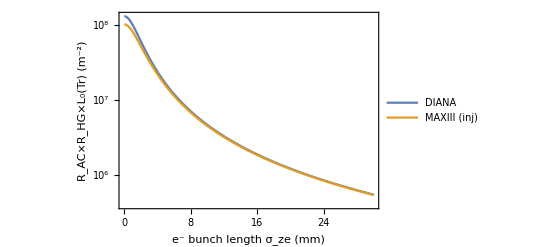

```mathematica
ListLogPlot[{Partition[Riffle[RACRHGL0σze⟦All,1⟧,RACRHGL0σze⟦All,2⟧],2],Partition[Riffle[RACRHGL0σze⟦All,1⟧,RACRHGL0σze⟦All,3⟧],2]},Joined->{True,True},PlotRange->Full,Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_AC×R_HG×L_0(Tr) (m^-2)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.75,0.7}]]
```

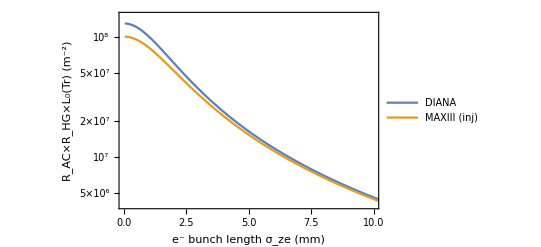

```mathematica
ListLogPlot[{Partition[Riffle[RACRHGL0σze⟦All,1⟧,RACRHGL0σze⟦All,2⟧],2],Partition[Riffle[RACRHGL0σze⟦All,1⟧,RACRHGL0σze⟦All,3⟧],2]},Joined->{True,True},PlotRange->{{0,10},{4*10^6,1.5*10^8}},Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_AC×R_HG×L_0(Tr) (m^-2)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII (inj)"},LabelStyle->12,LegendFunction->frame],{0.75,0.7}]]
```

These plots show that there is an advantage inherent in DIANA’s smaller transverse size in terms of luminosity when the hourglass effect, angular crossing effect and transverse luminosity. It is important to note that the crossing angle is identical for both ϕ = 5°, but that bunch length operating points are very different σ_ze = 1 mm (DIANA) and σ_ze = 26.7 mm (MAXIII) therefore a factor of 100 difference or so is seen by these effects. Consequently an long bunch accelerator will always be at a disadvantage  in terms of luminosity. This can either be accounted for by having a larger bunch charge or some kind of bunch compression/decompression scheme book-ending the IP.

## Transverse Effect (R_AC×R_HG×L_0) (Corrections Plus Original Dependence) (Transverse Beam Size)

```mathematica
RACRHGL0Trϕ=Table[{ϕ/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ10,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ1,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ01},{ϕ,0.1mrad,40mrad,0.1mrad}];
```

```mathematica
RACRHGL0Trσze=Table[{σze/mrad,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ10,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ1,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]*L0Tr[βIP,0,Ee,ϵn,σL]/.CBETAβ01},{σze,c*0.1ps,c*100ps,c*0.1ps}];
```

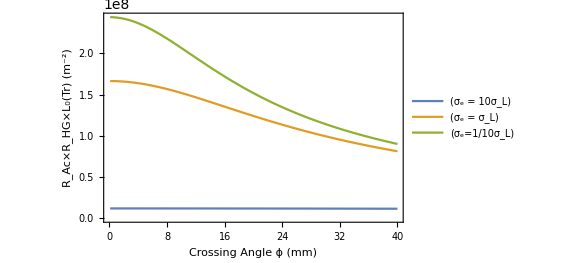

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGL0Trϕ⟦All,1⟧,RACRHGL0Trϕ⟦All,2⟧],2],Partition[Riffle[RACRHGL0Trϕ⟦All,1⟧,RACRHGL0Trϕ⟦All,3⟧],2],Partition[Riffle[RACRHGL0Trϕ⟦All,1⟧,RACRHGL0Trϕ⟦All,4⟧],2]},PlotRange->Full,Frame->True,FrameLabel->{"Crossing Angle ϕ (mm)","R_Ac×R_HG×L_0(Tr) (m^-2)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.8,0.75}]]
```

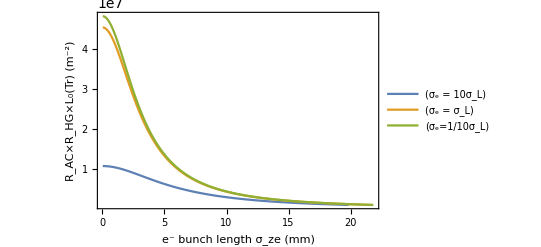

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGL0Trσze⟦All,1⟧,RACRHGL0Trσze⟦All,2⟧],2],Partition[Riffle[RACRHGL0Trσze⟦All,1⟧,RACRHGL0Trσze⟦All,3⟧],2],Partition[Riffle[RACRHGL0Trσze⟦All,1⟧,RACRHGL0Trσze⟦All,4⟧],2]},PlotRange->{{0,10},{5*10^7,1*10^6}},Frame->True,FrameLabel->{"e^- bunch length σ_ze (mm)","R_AC×R_HG×L_0(Tr) (m^-2)"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"(σ_e = 10σ_L)","(σ_e = σ_L)","(σ_e=1/10σ_L)"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

Flux penalty for having an electron bunch transverse size much larger than the electron bunch transverse size is much larger than the gain from having one smaller. The hourglass and angular crossing effects are smaller for larger transverse beams but these effects are small in comparison to the overall luminosity transverse dependence. The hourglass effect is meaningful and should be included, once it can be suitably accounted for (non-round beams), it should be  included within optimisation.

# Y. Miyahara (Crossing Angle, Round Beam)

## Analytical Solution (Round Beams)

```mathematica
Simplify[Integrate[(H*Exp[-A/(B+F*x^2)*x^2-G/J*x^2])/(B+F*x^2),{x,-∞,∞}(*,Assumptions->{Element[{A,B,F,G,J},Reals],A>0,B>0,F>0,G>0,J>0}*)]]
```

Integrate[(ⅇ^(-x^2 (G/J+A/(B+F x^2))) H)/(B+F x^2),{x,-∞,∞},Assumptions→(A|B|F|G|J)∈ℝ&&A>0&&B>0&&F>0&&G>0&&J>0]

This is a simplified simplified version of Miyahara’s angular crossing + hourglass reduction factor for round beams i.e. the beams are identical in size in both x and y. Here A = sin^2(ϕ/2) (Miyahara’s crossing angle ϕ = ϕ/2 in our case), B =  <σ_RB^2> , the convoluted pulse + bunch transverse size squared, F = <U_RB^2>, the convoluted pulse + bunch divergence , x = Z_c, the original integration variable, G = cos^2(ϕ/2), J = <σ_z^2>, the convoluted bunch length and pulse length squared and H = cos(ϕ/2)(<σ_RB^2>)/(√π<σ_z^2>) .

## Miyahara Intermediaries

```mathematica
URB[βIP_,z_,Ee_,ϵn_,σL_,λ_]:=1/2*(σe[βIP,z,Ee,ϵn]^2/βIP^2+(4*σL)/zr[λ,σL]);
σRB[βIP_,z_,Ee_,ϵn_,σL_]:=σe[βIP,z,Ee,ϵn]^2+σL^2;
σz[σze_,σzL_]:=σze^2+σzL^2;
H[ϕ_,βIP_,z_,Ee_,ϵn_,σL_,σze_,σzL_]:=Cos[ϕ/2]*σRB[βIP,z,Ee,ϵn,σL]/Sqrt[π*σz[σze,σzL]];
```

## Reduction Factor Calculation (WRONG - FUCKED UP ANALYTICAL CALC)

```mathematica
RACHG[βIP_,z_,Ee_,ϵn_,σL_,ϕ_,λ_,σze_,σzL_]:=(Exp[(σRB[βIP,z,Ee,ϵn,σL]*(Sin[ϕ/2]^2/(σRB[βIP,z,Ee,ϵn,σL]+URB[βIP,z,Ee,ϵn,σL,λ])+Cos[ϕ/2]^2/σz[σze,σzL]))/URB[βIP,z,Ee,ϵn,σL,λ]]*H[ϕ,βIP,z,Ee,ϵn,σL,σze,σzL]*π*Erfc[Sqrt[(σRB[βIP,z,Ee,ϵn,σL]*(Sin[ϕ/2]^2/(σRB[βIP,z,Ee,ϵn,σL]+URB[βIP,z,Ee,ϵn,σL,λ])+Cos[ϕ/2]^2/σz[σze,σzL]))/URB[βIP,z,Ee,ϵn,σL,λ]]])/Sqrt[σRB[βIP,z,Ee,ϵn,σL]*URB[βIP,z,Ee,ϵn,σL,λ]];
```

```mathematica
RACHG[βIP,0,Ee,ϵn,σL,ϕ,λ,σze,σzL]/.CBETA150
RACHG[βIP,0,Ee,ϵn,σL,ϕ,λ,σze,σzL]/.DIANA680
RACHG[βIP,0,Ee,ϵn,σL,ϕ,λ,σze,σzL]/.MAXIIIinjopt
```

0.166574

0.241631

0.0371988

## Angular Variation (R_ACHG IS CURRENTLY WRONG)

```mathematica
RACHGvsϕCBETA=Table[{ϕ/mrad,RACHG[βIP,0,Ee,ϵn,σL,ϕ,λ,σze,σzL]/.CBETA150,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETA150,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.CBETA150,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.CBETA150},{ϕ,0,40mrad,0.1mrad}];
```

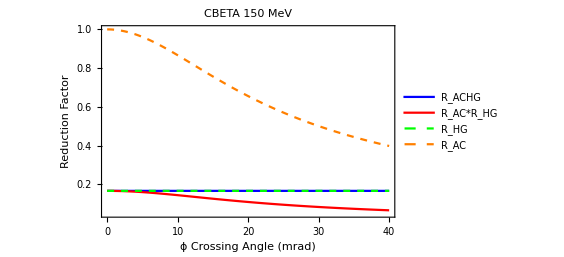

```mathematica
ListLinePlot[{Partition[Riffle[RACHGvsϕCBETA⟦All,1⟧,RACHGvsϕCBETA⟦All,2⟧],2],Partition[Riffle[RACHGvsϕCBETA⟦All,1⟧,RACHGvsϕCBETA⟦All,3⟧],2],Partition[Riffle[RACHGvsϕCBETA⟦All,1⟧,RACHGvsϕCBETA⟦All,4⟧],2],Partition[Riffle[RACHGvsϕCBETA⟦All,1⟧,RACHGvsϕCBETA⟦All,5⟧],2]},PlotRange->{{0,40},{0.05,1}},Frame->True,PlotLabel->"CBETA 150 MeV",FrameLabel->{"ϕ Crossing Angle (mrad)","Reduction Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"R_ACHG","R_AC*R_HG","R_HG","R_AC"},LabelStyle->12,LegendFunction->frame],{0.2,0.42}],PlotStyle->{Blue,Red,{Green,Dashed},{Orange,Dashed}}]
```

```mathematica
RACHGvsϕMAXIII=Table[{ϕ/mrad,RACHG[βIP,0,Ee,ϵn,σL,ϕ,λ,σze,σzL]/.MAXIIIinjopt,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]*RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt,RHG[βIP,0,Ee,ϵn,σL,σze,σzL,λ]/.MAXIIIinjopt,RACMiyahara[βIP,0,Ee,ϵn,σL,ϕ,σze,σzL]/.MAXIIIinjopt},{ϕ,0,40mrad,0.1mrad}];
```

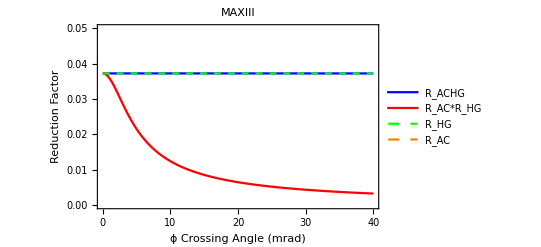

```mathematica
ListLinePlot[{Partition[Riffle[RACHGvsϕMAXIII⟦All,1⟧,RACHGvsϕMAXIII⟦All,2⟧],2],Partition[Riffle[RACHGvsϕMAXIII⟦All,1⟧,RACHGvsϕMAXIII⟦All,3⟧],2],Partition[Riffle[RACHGvsϕMAXIII⟦All,1⟧,RACHGvsϕMAXIII⟦All,4⟧],2],Partition[Riffle[RACHGvsϕMAXIII⟦All,1⟧,RACHGvsϕMAXIII⟦All,5⟧],2]},PlotRange->{{0,40},{0,0.05}},Frame->True,PlotLabel->"MAXIII",FrameLabel->{"ϕ Crossing Angle (mrad)","Reduction Factor"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"R_ACHG","R_AC*R_HG","R_HG","R_AC"},LabelStyle->12,LegendFunction->frame],{0.75,0.42}],PlotStyle->{Blue,Red,{Green,Dashed},{Orange,Dashed}}]
```

Clearly the angular part of R_ACHG is not functioning correctly.